```mathematica
200
```

```mathematica
WW1={{0.25,0.},{0.5,0.},{0.75,0.000014567943697710208},{1.,0.0034447222059790063},{1.25,0.04330941783040642},{1.5,0.18282574523916534},{1.75,0.4225754605361488},{2.,0.7234881458096027},{2.25,1.0520740071366217},{2.5,1.3644189791157117},{2.75,1.6083088670940577},{3.,1.8115899374627709}};
```

```mathematica
WW111=Interpolation[WW1];
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

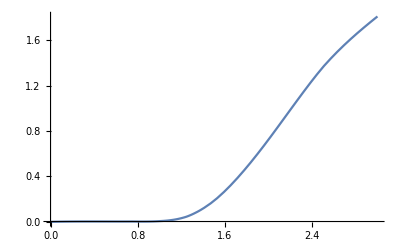

```mathematica
Plot[WW111[x],{x,0,3}]
```

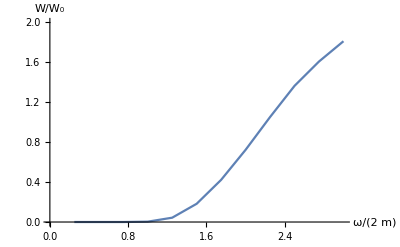

```mathematica
ListLinePlot[Re[WW1],PlotRange->{{0,3},{0,2}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

```mathematica
WW2={{0.25,0},{0.5,0},{0.75,0},{1,0},{1.25,0.0028873515320663214},{1.5,0.02006608146912996},{1.75,0.061456164744105854},{2,0.13354647259278238},{2.25,0.2395499246911103},{2.5,0.38118413161859693},{2.75,0.5520378291397025},{3,0.7573768484437469}};
```

```mathematica
WW222=Interpolation[WW2];
```

InterpolatingFunction::dmval: Input value TraditionalForm`{0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

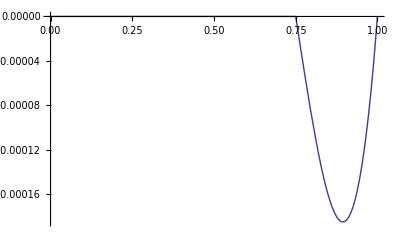

```mathematica
Plot[WW222[x],{x,0,1}]
```

```mathematica
Plot[{WW111[x]+WW222[x],WW1120[x]},{x,0,3},PlotStyle->{{Thick,Black},{Black,Thick,Dashed}},PlotRange->{{0,3},{0,5.5}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->{Bold,24}]
```

InterpolatingFunction::dmval: Input value TraditionalForm`{0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of TraditionalForm`InterpolatingFunction :: "dmval" will be suppressed during this calculation.

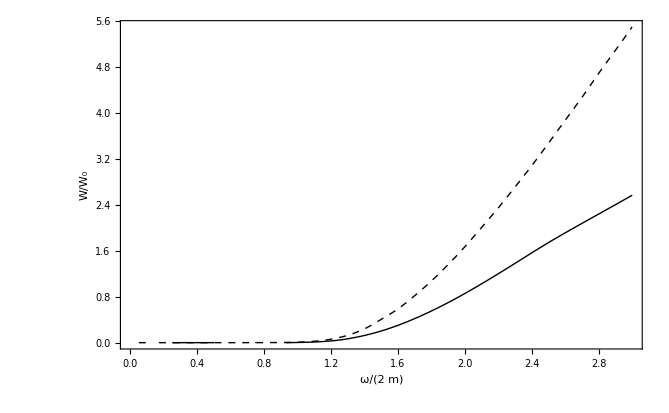

-Graphics-

```mathematica
Show[%,LabelStyle->Directive[FontFamily->"Times",FontSize->24, Black,Thin]]
```

-Graphics-

```mathematica
WW11={{1.5,-0.0903945908063515},{1.6,0.2483358535585939},{1.7000000000000002,0.39415449657148244},{1.8000000000000003,0.49558333690312023},{1.9000000000000004,0.6077656364639598},{2.0000000000000004,0.7051933173131911},{2.05,0.6744583266777819},{2.0599999999999996,0.6551928977953217},{2.0699999999999994,0.7167646106942468},{2.079999999999999,0.7977986727128236},{2.089999999999999,0.6722090548030591},{2.11,0.7230537624061025},{2.1500000000000005,0.6700977267055457},{2.2000000000000006,0.7972428584761548},{2.3000000000000007,0.7052017832918375},{2.400000000000001,0.8435497519545393},{2.500000000000001,0.7924093538014908},{2.600000000000001,0.8357538787448574},{2.700000000000001,0.7647891374312247},{2.800000000000001,0.7549686055024432},{2.9,0.7329140724184086},{3,0.7126941610105193}};
```

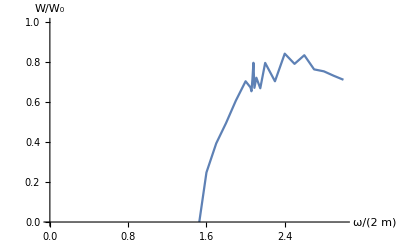

```mathematica
ListLinePlot[Re[WW11],PlotRange->{{0,3},{0,1}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

```mathematica
WW11F={{0.1,0},{0.2,0},{0.30000000000000004,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.7999999999999999,0},{0.8999999999999999,0},{0.9999999999999999,0},{1.0999999999999999,0},{1.2,0},{1.3,0},{1.4000000000000001,0},{1.45,0},{1.48,0},{1.5000000000000002,0},{1.6,0.2},{1.7000000000000002,0.39415449657148244},{1.8000000000000003,0.49558333690312023},{1.9000000000000004,0.6077656364639598},{2.0000000000000004,0.7051933173131911},{2.05,0.75},{2.0599999999999996,0.76},{2.0699999999999994,0.76},{2.079999999999999,0.767},{2.089999999999999,0.770},{2.11,0.777},{2.1500000000000005,0.780},{2.2000000000000006,0.789},{2.3000000000000007,0.791},{2.400000000000001,0.789},{2.500000000000001,0.782},{2.700000000000001,0.7647891374312247},{2.800000000000001,0.7549686055024432},{2.9,0.7329140724184086},{3,0.7126941610105193}};
WWW11F=Interpolation[WW11F];
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

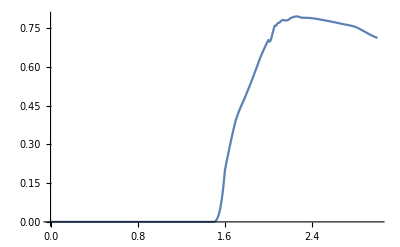

```mathematica
Plot[WWW11F[x],{x,0,3}]
```

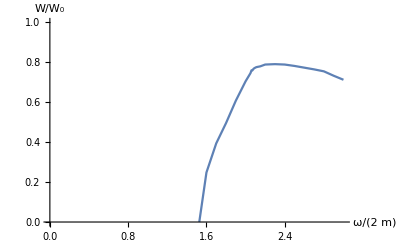

```mathematica
ListLinePlot[Re[WW11F],PlotRange->{{0,3},{0,1}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

```mathematica
WW12={{0,0},{0.1,0},{0.2,0},{0.30000000000000004,0},{0.4,0},{0.5,0},{0.6,0},{0.7,0},{0.7999999999999999,0},{0.8999999999999999,0},{0.9999999999999999,0},{1.0999999999999999,0},{1.2,0},{1.3,0},{1.4000000000000001,0},{1.5,0.},{1.6,0.005394597807986752},{1.6500000000000001,0.01125604846524923},{1.7000000000000002,0.01689560689904321},{1.7500000000000002,0.02232463430161049},{1.8000000000000003,0.029561501322917405},{1.8500000000000003,0.036690489817501504},{1.9000000000000004,0.044219275017994025},{1.9500000000000004,0.05483070826934961},{1.96,0.057625042260120794},{1.97,0.060325512661342014},{1.98,0.06570346729612422},{1.99,0.08136411654907315},{2.0000000000000004,0.09320629588411856},{2.01,0.07315219575396922},{2.0199999999999996,0.06794213862676614},{2.0299999999999994,0.06495677271009238},{2.039999999999999,0.06293952605791017},{2.0500000000000003,0.061513536507650776},{2.1000000000000005,0.05802520887103016},{2.1500000000000004,0.05700207181237047},{2.2000000000000006,0.05696754918296641},{2.2500000000000004,0.05742243276041893},{2.3000000000000007,0.058113394006937553},{2.3500000000000005,0.058991126640211694},{2.400000000000001,0.06002775626613744},{2.4500000000000006,0.06110686294994759},{2.500000000000001,0.06224483443300219},{2.5500000000000007,0.06339519276032089},{2.600000000000001,0.06456892421370547},{2.650000000000001,0.06572314526985011},{2.700000000000001,0.0668751682257856},{2.750000000000001,0.06801726329682767},{2.800000000000001,0.06916101097391622},{2.850000000000001,0.07028535896671412},{2.9,0.0713500454033167},{2.950000000000001,0.07241163997888625},{3.,0.07347178389879548}};
```

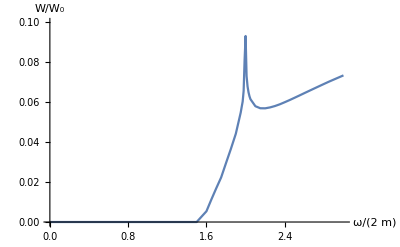

```mathematica
ListLinePlot[Re[WW12],PlotRange->{{0,3},{0,0.1}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

```mathematica
WWW12=Interpolation[WW12];
```

Interpolation::innd: First argument in TraditionalForm`WW12 does not contain a list of data and coordinates.

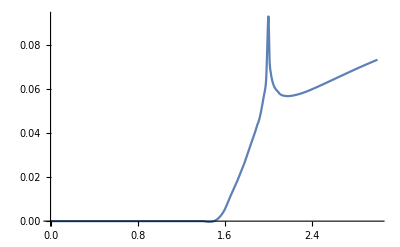

```mathematica
Plot[WWW12[x],{x,0,3}]
```

```mathematica
Plot[{WWW11F[x]+2WWW12[x],WW1220[x]},{x,0,3},PlotStyle->{{Thick,Black},{Black,Thick,Dashed}},PlotRange->{{0,3},{0,5.5}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->{Bold,24}]
```

InterpolatingFunction::dmval: Input value TraditionalForm`{0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

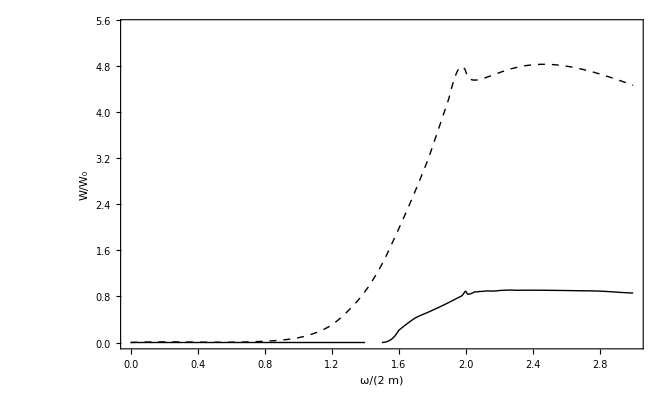

-Graphics-

```mathematica
Show[%,LabelStyle->Directive[FontFamily->"Times",FontSize->24, Black,Thin]]
```

-Graphics-

```mathematica
W1120={{0.05,10^-10},{0.1,10^-8},{0.2,3.1032344993990053*^-7},{0.30000000000000004,4.6102354289524425*^-6},{0.4,0.00001537197206579578},{0.5,0.00004703957316374673},{0.6,0.0001577674394067096},{0.7,0.0004529098247421124},{0.7999999999999999,0.00115753743847531},{0.8999999999999999,0.003179949845080662},{0.9999999999999999,0.008840491060867178},{1.0999999999999999,0.024253515174406142},{1.2,0.061087139911119956},{1.3,0.12938733948170733},{1.4000000000000001,0.24171440679931155},{1.5000000000000002,0.40818381763102807},{1.6000000000000003,0.5886981102453963},{1.7000000000000004,0.8199533175872066},{1.8000000000000005,1.0747861496258417},{1.9000000000000006,1.3614293068604102},{2.0000000000000004,1.67134368332595},{2.1000000000000005,2.009882056758594},{2.2000000000000006,2.3495560349124514},{2.3000000000000007,2.7147124631657893},{2.400000000000001,3.08437596812088},{2.500000000000001,3.4766634544255415},{2.600000000000001,3.8786905193173293},{2.700000000000001,4.273427690789159},{2.800000000000001,4.694384433496369},{2.9000000000000012,5.095760825564574},{3.0000000000000013,5.505035334089248},{3.1000000000000014,6.013242972101808},{3.2000000000000015,6.40772445586207},{3.3000000000000016,6.883784391324107},{3.4000000000000017,7.295359194033462},{3.5000000000000018,7.774030850852736},{3.600000000000002,8.208843860121023},{3.700000000000002,8.65762476254783},{3.800000000000002,9.15118040669512},{3.900000000000002,9.452325743521628},{4.000000000000002,10.074921381025561},{4.100000000000001,10.284470807297023},{4.200000000000001,10.787100085427623},{4.300000000000001,11.259940335189718},{4.4,11.69763814925251},{4.5,11.94680501284228},{4.6,12.407817171994353},{4.699999999999999,12.774642720511565},{4.799999999999999,13.413909402712644},{4.899999999999999,13.73851975131529},{4.999999999999998,14.593224173312473},{5.099999999999998,14.650153190146158},{5.1999999999999975,15.52989987908525},{5.299999999999997,15.472907967234457},{5.399999999999997,16.059272988707008},{5.4999999999999964,16.054584290008357},{5.599999999999996,16.5782957043035},{5.699999999999996,17.09979429574996},{5.799999999999995,17.369162131750382},{5.899999999999995,18.09777272113117},{5.999999999999995,18.854366315341604},{6.099999999999994,18.93685022977846},{6.199999999999994,19.458440024862504},{6.299999999999994,20.585355339690775},{6.399999999999993,20.28794534767399},{6.499999999999993,20.529280400738102},{6.5999999999999925,20.896779781131574},{6.699999999999992,21.87415340223639},{6.799999999999992,22.009331558606398},{6.8999999999999915,22.17137052321171},{6.999999999999991,23.6857783308232}};
```

```mathematica
WW1120=Interpolation[W1120];
```

```mathematica
W1220={{0,0},{0.7,0.010035537951455294},{0.7999999999999999,0.021736922457305144},{0.8999999999999999,0.04212328195265349},{0.9999999999999999,0.08250694386755006},{1.0999999999999999,0.1639390597960392},{1.2,0.304806758568705},{1.3,0.5556621153405457},{1.4000000000000001,0.8876531415092384},{1.5000000000000002,1.3584792874634743},{1.6000000000000003,1.9723757919068454},{1.7000000000000004,2.6379991232313493},{1.8000000000000005,3.369547597645867},{1.9000000000000006,4.24200547113719},{1.99,4.767829320087826},{2.001,4.707490588815143},{2.01,4.628783056678078},{2.0199999999999996,4.592581785117515},{2.0299999999999994,4.573704103155265},{2.039999999999999,4.56423316479814},{2.049999999999999,4.560558854763991},{2.0599999999999987,4.560877689504516},{2.0699999999999985,4.563962824870416},{2.0799999999999983,4.569407891520388},{2.089999999999998,4.576475830619513},{2.099999999999998,4.584628454030864},{2.1099999999999977,4.593611926211753},{2.15,4.634891514515171},{2.2,4.688358021300629},{2.3000000000000003,4.777225210955083},{2.4000000000000004,4.8262018420289685},{2.5000000000000004,4.832872977366396},{2.6000000000000005,4.803427752041745},{2.7000000000000006,4.7458266182531785},{2.8000000000000007,4.667299540954054},{2.900000000000001,4.57340875455622},{3.000000000000001,4.469796038440462},{3.100000000000001,4.35974832105122},{3.200000000000001,4.2466096345774655},{3.300000000000001,4.135361196603401},{3.4000000000000012,4.027516282006917},{3.5000000000000013,3.9226395670334564},{3.6000000000000014,3.8221086864771388},{3.7000000000000015,3.7251492847262933},{3.8000000000000016,3.6325672459301583},{3.9000000000000017,3.542878955906887},{4.000000000000002,3.4559074407629926},{4.100000000000001,3.371905281727157},{4.200000000000001,3.2895410864713766},{4.300000000000001,3.2093556400007577},{4.4,3.1310150846738716},{4.5,3.054126121671722},{4.6,2.97993497869517},{4.699999999999999,2.907956830504711},{4.799999999999999,2.838813446149133},{4.899999999999999,2.772275247457617},{4.999999999999998,2.707944221759527},{5.099999999999998,2.646531491963387},{5.1999999999999975,2.5865525329198067},{5.299999999999997,2.5297746866713573},{5.399999999999997,2.475079574697711},{5.4999999999999964,2.4229307637801445},{5.599999999999996,2.3721134875905197},{5.699999999999996,2.323474716366196},{5.799999999999995,2.276381308696599},{5.899999999999995,2.2316220738199966},{5.999999999999995,2.188305263754071},{6.099999999999994,2.146768108677844},{6.199999999999994,2.107042158053642},{6.299999999999994,2.068304549898288},{6.399999999999993,2.0317043512646253},{6.499999999999993,1.9968309927028556},{6.5999999999999925,1.9622742484525033},{6.699999999999992,1.9291343248969637},{6.799999999999992,1.8978510516876317},{6.8999999999999915,1.8663199198439369},{6.999999999999991,1.8364774200984963}};
```

```mathematica
WW1220=Interpolation[W1220];
```

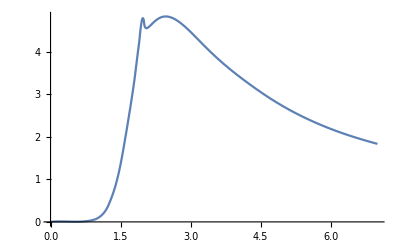

```mathematica
Plot[WW1220[x],{x,0,7}]
```

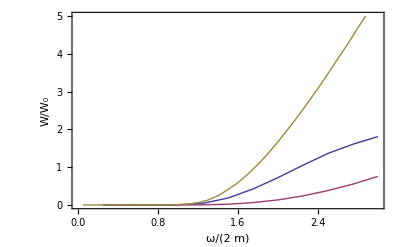

```mathematica
ListLinePlot[{WW1,WW2,Re[W1120]},Frame->True,PlotRange->{{0,3},{0,5}},RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]}]
```